## Kapitola 5 - RBF síť a Iris data

Demonstrace použití RBF sítě na datech z databáze UCI.

## Inicializace knihovny NeuralNetworks

Nejprve načteme knihovnu pro neuronové sítě.

```mathematica
<<NeuralNetworks`
```

Pokud pracujete v Mathematice 8.0, vypněte ještě zobrazování chybové hlášky Remove::rmnsm. Tuto hlášku vyhazují funkce knihovny NeuralNetworks. Na funkci knihovny toto nemá žádný vliv.

```mathematica
Off[Remove::rmnsm];
```

## Import dat

### Načtení dat ze souboru

Nastavíme si pracovní adresář na ten, kde máme uložen aktuální notebook, načítaná data musejí být ve stejném adresáři.

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Dokumenty\ŠKOLA\ČVUT\BP\BP_Neuron

```mathematica
data=Import["iris.data"];
```

### Načtení dat přímo z internetu

Jiná možnost je importovat data přímo z internetu - příklad pro UCI databázi (stejná data jako v předchozím příkladu - načtení dat ze souboru).

```mathematica
data=Import["http://ftp.ics.uci.edu/pub/machine-learning-databases/iris/iris.data"];
```

## Předzpracování dat

Předzpravování dat provedeme pomocí stejného postupu, který je popsán v kapitole “Dopředná síť a Iris data”.

```mathematica
data2=Drop[data,-1];
inData=data2[[All,1;;4]];(*vstupní parametry*)
outDataTmp=data2[[All,5]];(*výstupní parametr*)
outVal=Tally[outDataTmp][[All,1]];
encode=MapIndexed[#1->Normal[SparseArray[#2->1,{Length[outVal]}]]&,outVal];
outData=Flatten[outDataTmp]/.encode;
```

## Zpracování dat neuronovou sítí

Inicializace sítě - zadáme trénovací množinu, rozdělenou na vstupní a výstupní data, počet neuronů, případně můžeme zadat i aktivační funkci neuronu. Počet neuronů se zadává jako kladné celé číslo.

Vytvořenou síť si uložíme do proměnné "net".

```mathematica
net=InitializeRBFNet[inData,outData,4,Neuron->Sigmoid]
```

RBFNet[{{w1, λ, w2}, χ},{Neuron → Sigmoid, FixedParameters → None, AccumulatedIterations → 0, CreationDate → {2011, 4, 5, 13, 21, 48.5186553}, OutputNonlinearity → None, NumberOfInputs → 4}]

Můžeme si nechat zobrazit nějaké další informace o vytvořené síti.

```mathematica
NetInformation[net]
```

Radial Basis Function network. Created 2011-4-5 at 13:21. The network has 4 inputs and 3 outputs.  It consists of 4 basis functions of Sigmoid type. The network has a linear submodel.

Natrénujeme síť pomocí funkce "NeuralFit", které zadáme naší síť (proměnná "net"), trénovací množinu ("inData" a "outData") a počet učících kroků.

Funkce NeuralFit vyprodukuje naučenou síť a záznam o průběhu učení (může se hodit) - obě tyto návratové hodnoty si ukládáme (do proměnné "net2" a "record").

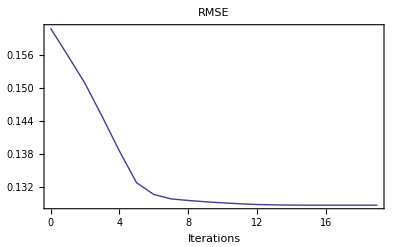

```mathematica
{net2,record}=NeuralFit[net,inData,outData,20];
```

Máme síť naučenou a můžeme se podívat na to, jak odpovídala během učení. Síť má 3 výstupy, proto následující příkaz vyprodukuje 3 grafy. Kadždý graf ukazuje počet správně a špatně klasifikovaných dat dané třídy v průběhu učení.

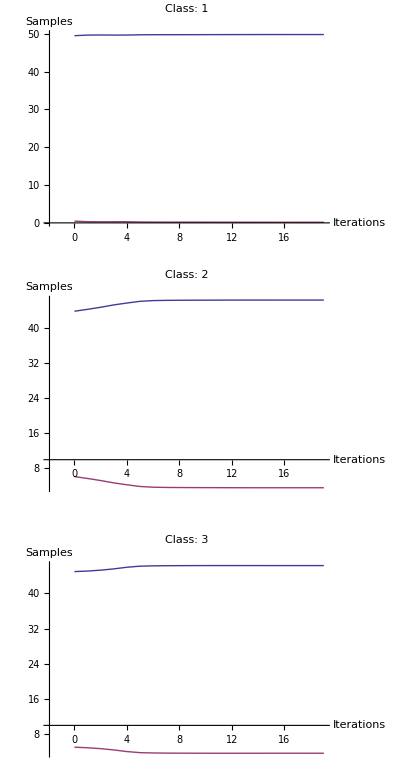

```mathematica
NetPlot[record,inData,outData,DataFormat->ClassPerformance]
```

Můžeme se podívat na klasifikaci pomocí "data/model" diagramu. Graf je interaktivní - pomocí myši ho můzeme otáčet, posouvat (Shift + myš) a zoomovat (Ctrl + myš). Čím víšší hodnoty jsou na diagonále, tím vyšší je úspěšnost klasifikace.

```mathematica
NetPlot[net2,inData,outData,DataFormat->BarChart]
```

-Graphics3D-

Jak se vyvíjela klasifikace se dá zobrazit stejným příkazem, akorát místo naučené síťě (net2) zadáme funkci NetPlot proměnnou "record" se záznamem o průběhu učení.

```mathematica
NetPlot[record,inData,outData,DataFormat->BarChart]
```

-Graphics-

Síť je možné si nechat symbolicky vyhodnotit - pro větší sítě je to ale už zcela nepřehledné, nicméně aktivační funkce tam zcela jistě poznáte.

Síť funguje v Mathematice jako klasická funkce, takže ji můžeme dávat parametry - včetně symbolů.

```mathematica
net2[{x1,x2,x3,x4}]
```

{-6.558+0.867245/(1+ⅇ^(0.698546 (-5.7839+x1)^2+0.698546 (-2.3972+x2)^2+0.698546 (-5.1264+x3)^2+0.698546 (-2.23339+x4)^2))-37.5547/(1+ⅇ^(0.071385 (-5.68662+x1)^2+0.071385 (-2.16333+x2)^2+0.071385 (-4.14245+x3)^2+0.071385 (-2.14918+x4)^2))-0.141901/(1+ⅇ^(1.16071 (-6.27421+x1)^2+1.16071 (-2.99364+x2)^2+1.16071 (-4.72845+x3)^2+1.16071 (-0.879241+x4)^2))+64.124/(1+ⅇ^(0.0364373 (-6.54034+x1)^2+0.0364373 (-2.23314+x2)^2+0.0364373 (-4.65558+x3)^2+0.0364373 (-0.746528+x4)^2))-0.969095 x1-0.0257542 x2-0.742398 x3+1.50772 x4,12.292-3.15718/(1+ⅇ^(0.698546 (-5.7839+x1)^2+0.698546 (-2.3972+x2)^2+0.698546 (-5.1264+x3)^2+0.698546 (-2.23339+x4)^2))+59.9083/(1+ⅇ^(0.071385 (-5.68662+x1)^2+0.071385 (-2.16333+x2)^2+0.071385 (-4.14245+x3)^2+0.071385 (-2.14918+x4)^2))+2.07193/(1+ⅇ^(1.16071 (-6.27421+x1)^2+1.16071 (-2.99364+x2)^2+1.16071 (-4.72845+x3)^2+1.16071 (-0.879241+x4)^2))-101.276/(1+ⅇ^(0.0364373 (-6.54034+x1)^2+0.0364373 (-2.23314+x2)^2+0.0364373 (-4.65558+x3)^2+0.0364373 (-0.746528+x4)^2))+1.46865 x1+0.0921982 x2+0.914408 x3-2.44375 x4,-4.73403+2.28994/(1+ⅇ^(0.698546 (-5.7839+x1)^2+0.698546 (-2.3972+x2)^2+0.698546 (-5.1264+x3)^2+0.698546 (-2.23339+x4)^2))-22.3536/(1+ⅇ^(0.071385 (-5.68662+x1)^2+0.071385 (-2.16333+x2)^2+0.071385 (-4.14245+x3)^2+0.071385 (-2.14918+x4)^2))-1.93003/(1+ⅇ^(1.16071 (-6.27421+x1)^2+1.16071 (-2.99364+x2)^2+1.16071 (-4.72845+x3)^2+1.16071 (-0.879241+x4)^2))+37.1519/(1+ⅇ^(0.0364373 (-6.54034+x1)^2+0.0364373 (-2.23314+x2)^2+0.0364373 (-4.65558+x3)^2+0.0364373 (-0.746528+x4)^2))-0.499551 x1-0.066444 x2-0.17201 x3+0.936028 x4}

## Prohlášení

Tento text je součástí bakalářské práce Adama Činčury “Demonstrační aplikace pro podporu kurzu neuronových sítí” na FEL ČVUT 2011. Vznikl úpravou textu Petra Chlumského.